```mathematica
SetDirectory[NotebookDirectory[]];
```

### init

```mathematica
SetOptions[#,
AxesStyle->Directive[Black,AbsoluteThickness[0.9]],
LabelStyle->Directive[Black,FontFamily->"CMU Serif",FontSize->16],
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[0.9],FontFamily->"CMU Serif",FontSize->13,FontSlant->Plain],
PlotRangePadding->{None,Automatic},
ImageSize->400
]&/@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,ListLinePlot};
```

```mathematica
SetOptions[#,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]]
]&/@{Framed};
```

```mathematica
Attributes[myStyle]={Listable};
SetAttributes[myStyle,HoldAllComplete];
myStyle[form_,others___]:=Style[TraditionalForm[HoldForm[form]],others,FontFamily->"CMU Serif"];
```

### Basic Functions

```mathematica
NQ=NumberQ[N[#]]&;
```

```mathematica
Attributes[cLangNumberForm]={Listable};
Options[cLangNumberForm]={nDigits->2};
cLangNumberForm[x_,OptionsPattern[]]:=
If[NumericQ[x],
NumberForm[x//N,OptionValue[nDigits]+1,ExponentFunction->(If[#==0,Null,#]&),
NumberFormat->(Row[{
ToString[NumberForm[ToExpression[#1],{15,OptionValue[nDigits]}]],
"e",
If[#3=="","+00",If[Abs[ToExpression[#3]]>=10,If[ToExpression[#3]<0,"-","+"]<>ToString[Abs[ToExpression[#3]]],If[ToExpression[#3]<0,"-0","+0"]<>ToString[Abs[ToExpression[#3]]]]]}]&)]//ToString,
x];
```

```mathematica
cLangNumberForm[{{123124,1.},{123,123*^67}},nDigits->3]
```

{{1.231e+05,1.000e+00},{1.230e+02,1.230e+69}}

### initialize

```mathematica
eV=1;
GeV=10^9 eV;
keV=10^-6 GeV;
(*eV=10^-9 GeV;*)
cm=(5.0677307165483375*^13)/GeV;
meter=100cm;
μm=10^-6 meter;
sec=(1.5192674479961274*^24)/GeV;
kg=5.609588606807705*^26 GeV;
gram=10^-3 kg;
Kelvin=8.617333262000001*^-14 GeV;
```

```mathematica
ρχ=0.4 GeV/cm^3;
vχ0=10^-3;
```

```mathematica
mN=0.93149410372 GeV;
```

```mathematica
mass=300.939gram;
density=4.42 gram/cm^3;
volume=mass/density;
nucleonNumber=mass/mN;
Reffctive=(volume/(4π/3))^(1/3);(* 形状因子对形状依赖性弱，近似为球体来处理 *)
```

```mathematica
δnSquareBar=(7.29*10^22 cm^-3)^2;
nBar=2.688*10^24 cm^-3;
ξ=2μm;

FSq[q_]:=δnSquareBar/nBar^2(6 ξ^3)/(Reffctive^3(1+q^2 ξ^2)^2);
```

```mathematica
δa=4.8×10^−12;(* 与acc函数对应，去掉了单位 cm/sec^2 *)
```

坐标系：z轴竖直向上的球坐标系。与form factor中z相同。x轴沿摆中心到摆体的连线方向，与所观测加速度的方向的夹角定义为ϕacc。
基础变量：入射速度矢量(v_i,θ_i,ϕ_i)，出射方位角(θ_f,ϕ_f)。

```mathematica
angleVector3D[θ_,ϕ_]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
piVec[mχ_,vi_,θi_,ϕi_]:=mχ vi angleVector3D[θi,ϕi];
pfVec[mχ_,vi_,θf_,ϕf_]:=mχ vi angleVector3D[θf,ϕf];
qVec[mχ_,vi_,θi_,ϕi_,θf_,ϕf_]:=piVec[mχ,vi,θi,ϕi]-pfVec[mχ,vi,θf,ϕf];

viVec[vi_,θi_,ϕi_]:=vi angleVector3D[θi,ϕi];
vfVec[vi_,θf_,ϕf_]:=vi angleVector3D[θf,ϕf];

(* 所观测的加速度方向在(x,y)平面中，与x轴夹角为ϕacc *)
accDirection[ϕacc_]:=angleVector3D[π/2,ϕacc];
qacc[mχ_,vi_,θi_,ϕi_,θf_,ϕf_,ϕacc_]:=qVec[mχ,vi,θi,ϕi,θf,ϕf].accDirection[ϕacc];
```

### velocity distribution

```mathematica
(* recommended in 2105.00599 *)
cIncms=29979245800;(*cm/s*)
cInkms=10^-5 cIncms;(*km/s*)
v0=238./cInkms;(* c *)
vEsc=544./cInkms; (* c *)
```

```mathematica
fHaloGalWithoutNorm[vGalNorm_]:=Exp[-vGalNorm^2/v0^2]UnitStep[vEsc-vGalNorm];
fHaloGalNorm=1/NIntegrate[4π fHaloGalWithoutNorm[vGalNorm] vGalNorm^2,{vGalNorm,0,vEsc}];
fHaloGalWithNorm[vGalNorm_]:=fHaloGalNorm Exp[-vGalNorm^2/v0^2]UnitStep[vEsc-vGalNorm];
```

```mathematica
4π NIntegrate[fHaloGalWithNorm[v] v^2,{v,0,vEsc}]
```

1.

according to Ref.2105.00599, neglect earth and solar peculiar velocity, 
v_gal=v_lab+v_0=v_χ+v_0.
Therefore,
f(v_gal)ⅆ^3 v_gal=f(v_χ+v_0)ⅆ^3 v_χ.

```mathematica
fHaloWithNorm[vχVec_,v0Vec_]:=fHaloGalWithNorm[Norm[vχVec+v0Vec]];
```

0.999978

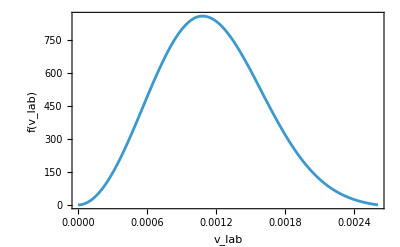

```mathematica
vχList=Subdivide[0,v0+vEsc,100];

v0VecHere=v0 angleVector3D[0,0];
fHaloLabTable=ParallelTable[
{vχ,NIntegrate[vχ^2 fHaloWithNorm[vχ angleVector3D[θ,ϕ],v0VecHere]Sin[θ],{θ,0,π},{ϕ,0,2π},PrecisionGoal->5,MaxRecursion->30]//Quiet},{vχ,vχList}];

NIntegrate[Interpolation[fHaloLabTable][x],{x,0,v0+vEsc}]
ListPlot[fHaloLabTable,Joined->True,FrameLabel->{"v_lab","f(v_lab)"}]
```

### Total Cross Section

```mathematica
dσtotdΩ[qVec_,σχN_?NQ]:=nucleonNumber^2 FSq[Norm[qVec]] σχN/(4π);
```

```mathematica
piVec2[pi_,θi_,ϕi_]:=pi angleVector3D[θi,ϕi];
pfVec2[pi_,θf_,ϕf_]:=pi angleVector3D[θf,ϕf];
qVec2[pi_,θi_,ϕi_,θf_,ϕf_]:=piVec2[pi,θi,ϕi]-pfVec2[pi,θf,ϕf];
```

### Acceleration

```mathematica
(* v0为地球运动的方向。 *)
(* 注意：取v0方向为观测加速度的反方向： *)
v0Vec[ϕacc_]:=v0 angleVector3D[π/2,ϕacc+π];
```

a=n_χ/m_target∫ⅆ^3 v_χⅆ Ω_χ' q_acc v_χ f(v_χ) (ⅆ σ_tot)/(ⅆ Ω_χ')=n_χ/m_target∫v_χ^2 Sin[θ_i]Sin[θ_f]ⅆ v_χⅆ θ_iⅆ ϕ_iⅆ θ_fⅆ ϕ_f q_acc v_χ f(v_χ) (ⅆ σ_tot)/(ⅆ Ω_χ').

```mathematica
accIntegrand0=Compile[{mχ,σχN,ϕacc,vi,θi,ϕi,θf,ϕf},
Module[{q,NA},
q=qVec[mχ,vi,θi,ϕi,θf,ϕf];

qacc[mχ,vi,θi,ϕi,θf,ϕf,ϕacc] vi fHaloWithNorm[viVec[vi,θi,ϕi],v0Vec[ϕacc]]
(dσtotdΩ[q,σχN])
(vi^2 Sin[θi]Sin[θf])

]//Evaluate(*,CompilationTarget->"C"*)
];
accIntegrand[mχ_?NQ,σχN_?NQ,ϕacc_?NQ,vi_?NQ,θi_?NQ,ϕi_?NQ,θf_?NQ,ϕf_?NQ]:=
accIntegrand0[mχ,σχN,ϕacc,vi,θi,ϕi,θf,ϕf];
```

```mathematica
Clear[acc];
acc[mχ_?NQ,σχN_?NQ,ϕacc_?NQ]:=
acc[mχ,σχN,ϕacc]=
1/(cm/sec^2)(ρχ/mχ)/mass Abs@NIntegrate[accIntegrand[mχ,σχN,ϕacc,vi,θi,ϕi,θf,ϕf],{vi,0,v0+vEsc},{θi,0,π},{ϕi,0,2π},{θf,0,π},{ϕf,0,2π},
PrecisionGoal->2,Method->{"AdaptiveQuasiMonteCarlo","MaxPoints"->10^6}
];
```

```mathematica
acc[1eV,1*^-38 cm^2,π/2]
```

1.59428×10^-12

```mathematica
acc[10eV,1*^-38 cm^2,π/2]
```

1.40446×10^-12

```mathematica
acc[5000eV,1*^-38 cm^2,π/2]
```

NIntegrate::maxp: 在 1000100 被积函数计算后，积分无法收敛. 对于积分和误差估计，NIntegrate 得到 0.392738 和 0.015191.

6.51325×10^-20

```mathematica
(* 监测每个核的计算 *)
kernels=ParallelTable[$KernelID->i,{i,$KernelCount}];
currentStep=ConstantArray[0,Length@kernels];
SetSharedVariable[kernels,currentStep];
```

```mathematica
findXSec[mχ_,ϕacc_,δa_]:=
Module[{referenceσχNIncm2,limitσχN,accResult},
referenceσχNIncm2=1.*10^-38;

currentStep[[$KernelID/.kernels]]=
"Kernel "<>ToString[$KernelID]<>": mχ = "<>cLangNumberForm[mχ]<>", σ = "<>cLangNumberForm[referenceσχNIncm2];

accResult=acc[mχ,referenceσχNIncm2 cm^2,ϕacc];
limitσχN=δa/accResult referenceσχNIncm2;

currentStep[[$KernelID/.kernels]]=
"Kernel "<>ToString[$KernelID]<>": mχ = "<>cLangNumberForm[mχ]<>", σ = "<>cLangNumberForm[limitσχN];

accResult=acc[mχ,limitσχN cm^2,ϕacc];
If[Abs[accResult/δa-1]<0.2,limitσχN,{"Check Again!",limitσχN}]
];
```

```mathematica
With[{ϕacc=π/2.},
filename="Data/MICROSCOPE/limits_MICROSCOPE.txt";

If[!FileExistsQ[filename],
mχPointNum=50;
mχMin=10;
mχMax=5000;
mχList={1}~Join~Exp@Subdivide[Log[mχMin],Log[mχMax],mχPointNum];
PrintTemporary@Dynamic[currentStep//Column];
limitMICROSCOPE=ParallelTable[{mχ/eV,findXSec[mχ,ϕacc,δa]},{mχ,mχList}];
Save[filename,{limitMICROSCOPE}];,
Get[filename];
];
]
```

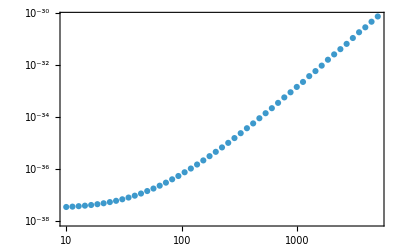

```mathematica
ListLogLogPlot[limitMICROSCOPE]
```

### Fig

```mathematica
<<MaTeX`;

(*tickForm[x_]:=If[StringQ[x],Text[Style[x,13,FontFamily->"CMU Serif"]],x];*)
myRange10[min_,max_]:=Module[{list},
list=10^Subdivide[Log[10,min],Log[10,max],Log[10,max/min]];
(Join@@Table[Range[list[[ii]],list[[ii+1]],list[[ii]]],{ii,Length[list]-1}])//DeleteDuplicates
];

longTick=0.015;
shortTick=1/2 longTick;

vTicks=myRange10[10^-50,10^-20];
leftTicks={
#,
If[Mod[Log[10,#],1]==0,myStyle[10]^myStyle[Log[10,#]]//ReleaseHold,Null],
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(vTicks);
rightTicks={
#,
Null,
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(vTicks);

hTicks=myRange10[10^-10,10^10];
bottomTicks={
#,
If[Mod[Log[10,#],1]==0,myStyle[10]^myStyle[Log[10,#]]//ReleaseHold,Null],
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(hTicks);
topTicks={
#,
Null,
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(hTicks);
```

```mathematica
frameLabel=MaTeX[#,FontSize->15]&/@{"m_\\chi \, [ \\mathrm{keV} ]","\\sigma_{\\chi N} \, [\\mathrm{cm}^{2}]"};
legendLabel=MaTeX[#,FontSize->9]&/@{"\\text{LUX-ZEPLIN}","\\text{Super-K}","\\text{PandaX-II}","\\text{CDEX-10}","\\text{Supernova Cooling}"};
MICROSCOPELabel=MaTeX["\\textbf{MICROSCOPE}",FontSize->16];
```

```mathematica
myColor1=RGBColor["#d5674f"]
myColor2=RGBColor["#4584D9"]
myColor3=RGBColor["#e48a00"]
myColor4=RGBColor["#5DA39D"]
myColor5=RGBColor["#9d7fa9"]
```

RGBColor[0.8352941176470589, 0.403921568627451, 0.30980392156862746]

RGBColor[0.27058823529411763, 0.5176470588235295, 0.8509803921568627]

RGBColor[0.8941176470588236, 0.5411764705882353, 0.]

RGBColor[0.36470588235294116, 0.6392156862745098, 0.615686274509804]

RGBColor[0.615686274509804, 0.4980392156862745, 0.6627450980392157]

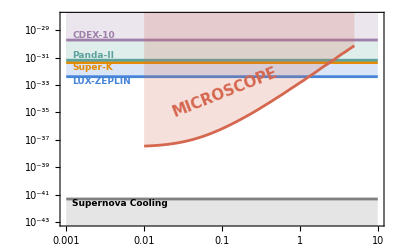

```mathematica
σLZ=4.0*10^-33;
σSK=4.3*10^-32;
σPandaX=6.4*10^-32;
σCDEX=1.9*10^-30;
σSupernova=4.7*10^-42;
limitMICROSCOPEMassinkeV=Times[#,{10^-3,1}]&/@limitMICROSCOPE;
Show[
LogLogPlot[
{σLZ,σSK,σPandaX,σCDEX},{x,10^-3,10^1},
FrameLabel->frameLabel,
PlotRange->{{10^-3,10^1},{10^-43,10^-28}},
PlotStyle->{myColor2,myColor3,myColor4,myColor5},
Filling->{1->{1,Lighter[myColor2,0.8]},2->{1,Lighter[myColor3,0.8]},3->{1,Lighter[myColor4,0.8]},4->{1,Lighter[myColor5,0.8]}},
FrameTicks->{{leftTicks,rightTicks},{bottomTicks,topTicks}}
],
LogLogPlot[
σSupernova,{x,10^-3,10^1},
PlotStyle->{Gray},
Filling->10^-50
],
ListLogLogPlot[limitMICROSCOPEMassinkeV,PlotStyle->myColor1,Joined->True,Filling->1],
Epilog->{
Inset[Rotate[myStyle["MICROSCOPE",15,myColor1,Bold],0.12π],Log/@{0.1,1 10^-33},{Center,Top}],
Inset[Rotate[myStyle["LUX-ZEPLIN",9,myColor2,Bold],0.π],Log/@{0.0012,σLZ},{Left,Top}],
Inset[Rotate[myStyle["Super-K",9,myColor3,Bold],0.π],Log/@{0.0012,σSK},{Left,Top}],
Inset[Rotate[myStyle["Panda-II",9,myColor4,Bold],0.π],Log/@{0.0012,σPandaX},{Left,Bottom}],
Inset[Rotate[myStyle["CDEX-10",9,myColor5,Bold],0.π],Log/@{0.0012,σCDEX},{Left,Bottom}],
Inset[Rotate[myStyle["Supernova Cooling",9,Bold],0.π],Log/@{0.0012,σSupernova},{Left,Top}]
}
]
```